```mathematica
init = CenterArray[1, {50, 50}] ;
s = ReplacePart[init, {24, 25}->1];
ArrayPlot@s
```

-Graphics-

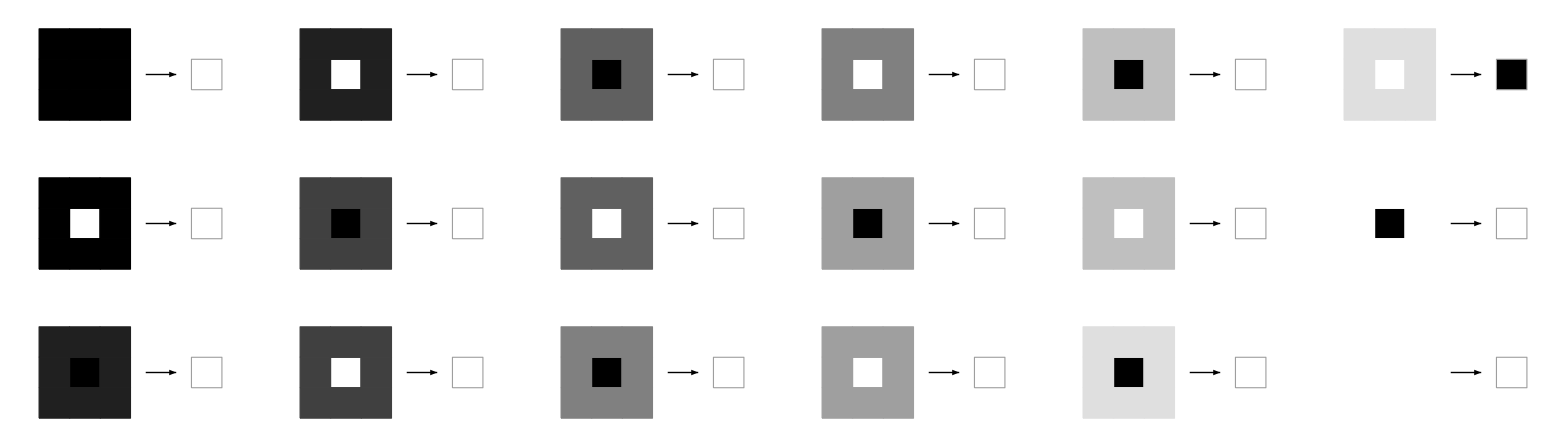

```mathematica
RulePlot[CellularAutomaton[<|"Dimension"->2,"OuterTotalisticCode"->4|>]]
```

```mathematica
ArrayPlot@ReplacePart[s,RandomChoice@Position[CellularAutomaton[<|"Dimension"->2,"OuterTotalisticCode"->4|>,s, {{{1}}}], 1]-> 1]
```

-Graphics-

```mathematica
ArrayPlot@ReplacePart[s,RandomChoice@Position[CellularAutomaton[<|"Dimension"->2,"OuterTotalisticCode"->4|>,s, {{{1}}}], 1]-> 1]
```

-Graphics-